# Numerical study of Griffith's principle

Nicholas Wheeler
Reed College Physics Department
4 November 2009

```mathematica
Hyperlink["Griffiths' Theory","http://en.wikipedia.org/wiki/Fracture_mechanics"]
Hyperlink["Fracture Kinetics","http://books.google.com/books?id=UWmvMMtDZtEC&pg=PA20&lpg=PA20&dq=Griffiths+crack+growth&source=bl&ots=W0aeQB7pNA&sig=YvoWhaHBxirEyHvqO6_KUCRISpw&hl=en&ei=fnzySom4GY3asgP71LQd&sa=X&oi=book_result&ct=result&resnum=10&ved=0CDUQ6AEwCQ#v=onepage&q=&f=false"]
```

I take a simple 100-node grid

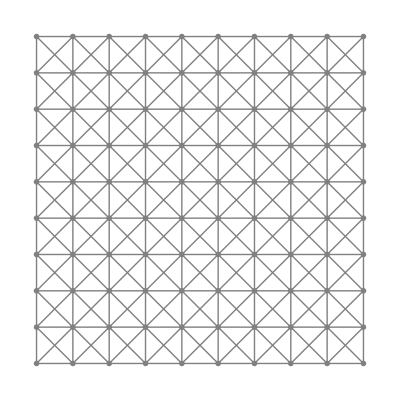

and displace each of the nodes in the 10th column 1.9 units to the right. I then release pins, one after another, starting at the lower right hand corner and progressing upward.  I then produce the following succession of deformed grids, on each of which I have superimposed the preceding image of the unstressed grid. Here is the fully stressed grid (no pins yet removed)

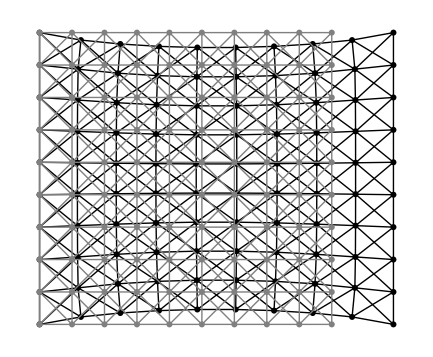

and now I inaugurate "crack growth" up the right side of the grid:

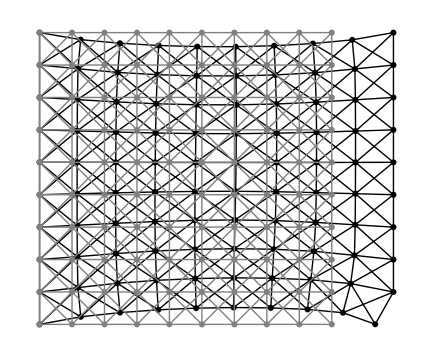

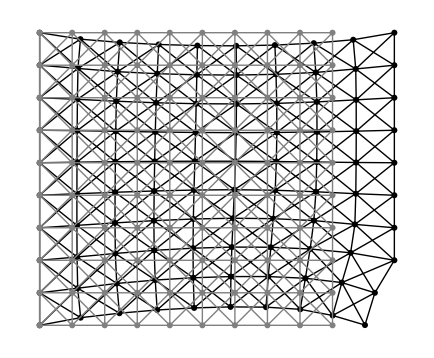

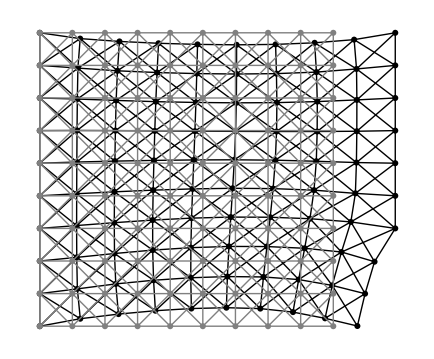

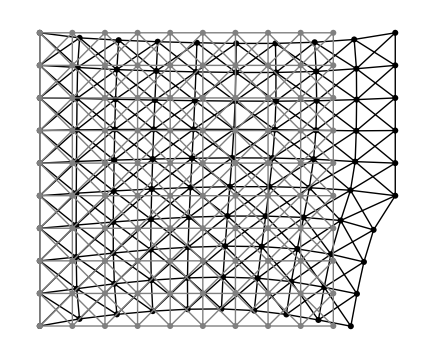

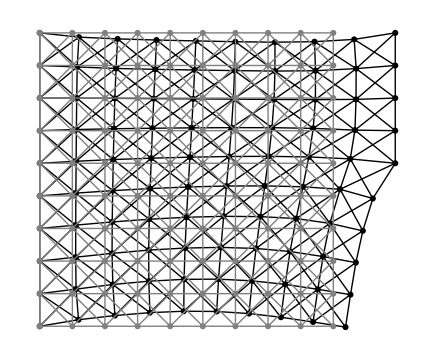

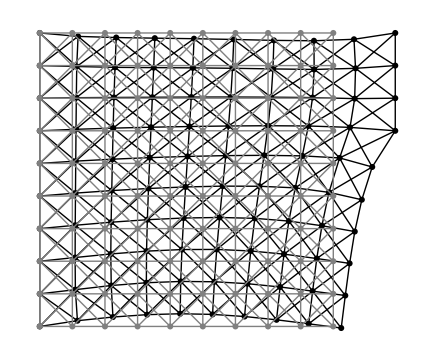

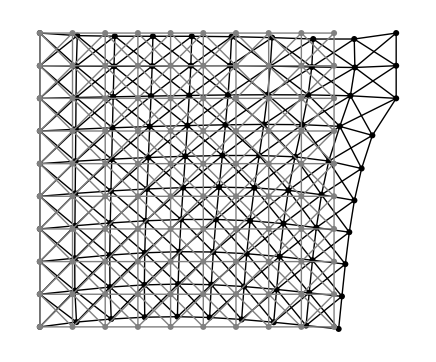

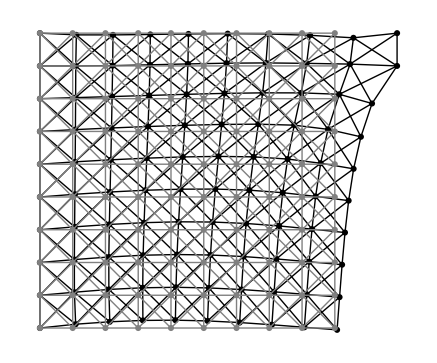

In each case I computed the energy ℰ_n stored in the spring system after n nodes had been released, and found ℰ_n to be a monotonically decreasing function of n (i.e., of crack length):

```mathematica
Table[{n,Subscript[ℰ, n]},{n,0,9}]//TableForm
```

0 | 6.38287
1 | 6.13977
2 | 5.79129
3 | 5.3767
4 | 4.91068
5 | 4.39968
6 | 3.84638
7 | 3.24886
8 | 2.59346
9 | 1.79619

I found, moreover, that the data conformed well to a quadratic function (as A. A. Griffith (1920) had speculated):

6.62837-0.199847 n-0.0280681 n^2

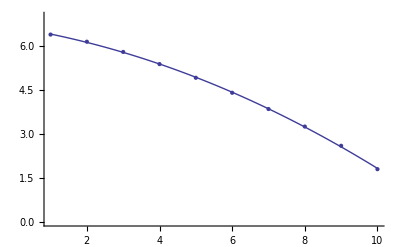

```mathematica
ℰ[n]
```

REMARK: Here the data point at 1 is the first data point, which is ℰ_0, not ℰ_1.

The spring energy released by crack-induced relaxation of the grid is

```mathematica
EnergyCredit[n_]:=ℰ[0]-ℰ[n]
```

```mathematica
EnergyCredit[n]
```

0.+0.199847 n+0.0280681 n^2

On the other hand, we expect the energy that must be invested to create a crack to depend linearly on crack length.

```mathematica
EnergyDebit[n_,strength_]:=-strength n
```

In the following figure (compare Gordon, page 101) I have set

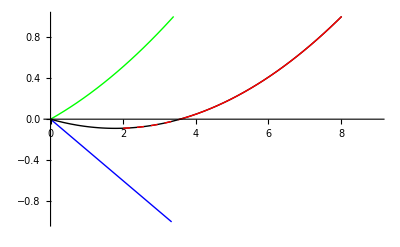

```mathematica
strength=0.3;
```

Energy credit is green, energy debit is blue, their sum is black/red. Looking to the figure, we see that the growth of cracks of length n ≲ 2 is unlikely, because it would cost the system energy. Growth is more likely if 2 ≲ n < 3.5,  and is catastrophically inevitable if n ≳ 3.5.